```mathematica
Quit[]
```

### Preliminary code & parameter input

```mathematica
(*specifies base directory to work in as notebook's directory*)
SetDirectory[NotebookDirectory[]];
(*
PARAMETER INPUT
*)
L=2000; (*upper bound for radius*)
T=1200; (*upper bound for time*)

L plot=L/5;(*plot up to Subscript[L, plot]<L*)
T plot=T/2;(*plot up to Subscript[T, plot]<T*)
t max=T;(*max time for validity plot*)

pts=2*10^4; (*number of points to use in spatial grid when using method of lines*)
tStep=1; (*maximal temporal step size when solving ODEs obtained from method of lines*)
		
dr=L/(2*10^3); (*radial step size for saving*)
dt=T/(2*10^3);  (*temporal step size for saving*)

doPlot=False; (*plot and save PDE solution plots*)
checkSol=False; (*plot and save PDE validity plots*)

(*
Variables to solve and save solution for appearing in same order as in ParametricNDSolve output function; ENTER AS LIST - ALL COMBINATIONS WILL BE EVALUATED
*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]

D ATP={346}; (*diffusion of ATP [μm^2/s]*)
D ADP={377}; (*diffusion of ADP [μm^2/s]*)
V cell={2414}; (*volume of cell [μm^3]*)
c0 ATP={5}; (*initial intracellular ATP concentration [×(10^-18)mol/μm^3] <---- UNITS ARE SCALED*)
c0 ADP=c0 ATP/10; (*initial intracellular ADP concentration [×(10^-18)mol/μm^3] <---- UNITS ARE SCALED*)
τ={15}; (*cell reseal time [s] -> range of 1-10*)
r0={0.1}; (*initial wound diameter [μm]*)
k1={0,0.000817,0.001683} (*5,10*); (*ATP->ADP degradation [s^-1]*)
k2={};  (*ADP degradation [s^-1]*)

(*
FUNCTION DEFINITIONS
*)
β[d_,w_,r0_]:=(4*d)/(5 (4/3 π w^3)) r0; 
f[w_][r_]:=UnitStep[w^2-r^2];
c in[d_,w_,c0_,τ_,r0_][t_]:=c0 E^(-((β[d,w,r0]τ)/Log[2])+(2^(-(t/τ)) β[d,w,r0]τ)/Log[2]);
(*3D parametric PDE to solve (spherical boundary & cell)*)
ATPpde[d_,w_,c0_,τ_,r0_,k_]:=(D[ATP[r,t], t]==d(D[ATP[r,t], r,r]+2/r D[ATP[r,t], r])+β[d,w,r0] 2^(-t/τ) c in[d,w,c0,τ,r0][t]*f[w][r]-k ATP[r,t]);
ADPpde[d_,w_,c0_,τ_,r0_,k1_,k2_]:=(D[ADP[r,t], t]==d(D[ADP[r,t], r,r]+2/r D[ADP[r,t], r])+β[d,w,r0] 2^(-t/τ) c in[d,w,c0,τ,r0][t]*f[w][r]+ATP[r,t]k1-ADP[r,t]k2);
```

### Batch export PDE solutions & plots

```mathematica
(*this function removes trailing decimals, which indicate floating point precision in Mathematica, and rounds irrational numbers down to 3 decimal places*)
(*NN[x_]:=If[StringLength[ToString[x]]>=5,ScientificForm[N[x],3,NumberFormat->(Row[{#1,"e",#3}]&)],ToString[x]];*)
NN[x_]:=If[Round[x]==x,ToString[Round@x],ToString[NumberForm[N[x,3],∞]]];
(*
Loop and save PDE solutions + plots 
*)
j=0; (*loop counter*)
Do[
k2 i=k1 i/4;
	(*make directory for saving solution if it doesn't exist*)		dirStr1=ToString[StringForm["D_``_``_V_``_c0_``_``_τ_``_r0_``_k_``_``",NN[D1 i],NN[D2 i],NN[V i],NN[c01 i],NN[c02 i],NN[tau i],NN[r0 i],NN[k1 i],NN[k2 i]]];
		dirStr2=ToString[StringForm["L_``_T_``_pts_``_tstep_``_dr_``_dt_``",NN[L],NN[T],NN[pts],NN[tStep],NN[dr],NN[dt]]];
		dir=FileNameJoin[{"runs",dirStr1,dirStr2}];
		
(*run iteration only if directory doesn't exist*)
If[DirectoryQ[dir],Continue[],
watch=AbsoluteTiming[
CreateDirectory[dir];

		(*solve PDE with given parameters*)
		w i=(3/(4π) V i)^(1/3);
		pdesolve=NDSolve[{ATPpde[D1 i,w i,c01 i,tau i,r0 i,k1 i],ADPpde[D2 i,w i,c02 i,tau i,r0 i,k1 i,k2 i],ATP[r,0]==0,ADP[r,0]==0,Derivative[1,0][ATP][L,t]==0,Derivative[1,0][ATP][-L,t]==0,Derivative[1,0][ADP][L,t]==0,Derivative[1,0][ADP][-L,t]==0},{ATP[r,t],ADP[r,t]},{r,-L,L},{t,0,T},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->{pts},"MinPoints"->{pts}}},MaxStepSize->tStep];
		ATPsol[r_,t_]:=Evaluate[ATP[r,t]/.pdesolve];
		ADPsol[r_,t_]:=Evaluate[ADP[r,t]/.pdesolve];

		(*sample solution uniformly*)
		ATPeval=Table[ATPsol[r i dr,t i dt][[1]],{r i,0,L/dr},{t i,0,T/dt}];
		ADPeval=Table[ADPsol[r i dr,t i dt][[1]],{r i,0,L/dr},{t i,0,T/dt}];
	
     (*export sampled solutions to .mat files*)
		Export[FileNameJoin[{dir,"data.mat"}],{"ATPsol"->ATPeval,"ADPsol"->ADPeval,"D_ATP"->{{D1 i}},"D_ADP"->{{D2 i}},"V_cell"->{{V i}},"c_0_ATP"->{{c01 i}},"c_0_ADP"->{{c02 i}},"tau_w"->{{tau i}},"r0"->{{r0 i}},"k1"->{{k1 i}},"k2"->{{k2 i}},"L"->{{L}},"T"->{{T}},"sp_pts"->{{pts}},"t_step"->{{tStep}},"dr"->{{dr}},"dt"->{{dt}}},"LabeledData"];
		
		(*write to log*)
		log=OpenAppend[FileNameJoin[{dir,"log"}]];
		WriteLine[log,DateString[]];
		WriteLine[log,"PDE solution saved."];
		Close[log];

(*plot solution if doPlot==True*)
		If[doPlot,
			(*radial contour plot of concentration*)
			ATPContour=ContourPlot[Evaluate[ATPsol[r,t]],{r,0,L plot},{t,0,T plot},AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->All,AxesLabel->Automatic];
			ADPContour=ContourPlot[Evaluate[ADPsol[r,t]],{r,0,L plot},{t,0,T plot},AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->All,AxesLabel->Automatic];
			(*export contour plots*)
			Export[FileNameJoin[{dir,"ATP_contour.png"}],ATPContour];
			Export[FileNameJoin[{dir,"ADP_contour.png"}],ADPContour];
			(*write to log*)
			log=OpenAppend[FileNameJoin[{dir,"log"}]];
			WriteLine[log,"PDE solution plotted."];
			Close[log];
		];

(*compute and plot validity plots if checkSol==True*)
		If[checkSol,
		(*check solution validity for ATP by comparing spatially integrated PDE solution to temporal ODE solution*)
			cATPode=NDSolve[{n'[t]==β[D1 i,w i,r0 i] 2^(-t/tau i) c in[D1 i,w i,c01 i,tau i,r0 i][t]V i-k1 i n[t],n[0]==0},n[t],{t,0,t max}];
			N ATP[t_]:=Evaluate[n[t]/.cATPode[[1]]];
		(*plot ATP validity plot*)		ATPCheck=Plot[{4π NIntegrate[ATPsol[r,t]r^2 ,{r,0,L},Method->{"InterpolationPointsSubdivision"(*,MaxSubregions->100*)}],N ATP[t]},{t,0,t max},AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution","ODE solution"},PlotStyle->{Dashed,Automatic},PlotLabel->"Validity of ATP concentration from PDE"];
		(*export ATP validity plot*)
		Export[FileNameJoin[{dir,"ATP_validity.png"}],ATPCheck];
			
(*check solution validity for ADP by comparing spatially integrated PDE solution to temporal ODE solution*)	cADPode=NDSolve[{n'[t]==β[D2 i,w i,r0 i]2^(-t/tau i) c in[D2 i,w i,c02 i,tau i,r0 i][t]V i+(Evaluate[n[t]/.cATPode[[1]]]) k1 i-k2 i n[t],n[0]==0},n[t],{t,0,t max}];
		N ADP[t_]:=n[t]/.cADPode[[1]];
		(*plot ADP validity plot*)ADPCheck=Plot[{4π NIntegrate[ADPsol[r,t]r^2 ,{r,0,L},Method->{"InterpolationPointsSubdivision"(*,MaxSubregions->100*)}],N ADP[t]},{t,0,t max},AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution","ODE solution"},PlotStyle->{Dashed,Automatic},PlotLabel->"Validity of ADP concentration from PDE"];
		(*export ADP validity plot*)
		Export[FileNameJoin[{dir,"ADP_validity.png"}],ADPCheck];
		];
];
	log=OpenAppend[FileNameJoin[{dir,"log"}]];
	WriteLine[log,ToString[StringForm["run `` finished after `` seconds\n",j+=1,ScientificForm[N[watch[[1]]],3,NumberFormat->(Row[{#1,"e",#3}]&)]]]];
WriteLine[log,ToString[StringForm["Kernel ID:``",$KernelID]]];
	Close[log];

];,
{D1 i,D ATP},{D2 i,D ADP},{V i,V cell},{c01 i,c0 ATP},{c02 i,c0 ADP},{tau i,τ},{r0 i,r0},{k1 i,k1}(*,{k2 i,k2}*)
];
```

$Aborted

```mathematica
(*(*specifies base directory to work in as notebook's directory*)
SetDirectory["C:\\Users\\Simon\\Dropbox (Personal)\\Research\\PhD\\research-projects\\atp-release\\local"];
(*
PARAMETER INPUT
*)
L=10^3/2; (*upper bound for radius*)
T=20; (*upper bound for time*)

L plot=L/5;(*plot up to Subscript[L, plot]<L*)
T plot=T/2;(*plot up to Subscript[T, plot]<T*)
t max=T;(*max time for validity plot*)

pts=2*10^4; (*number of points to use in spatial grid when using method of lines*)
tStep=0.1; (*maximal temporal step size when solving ODEs obtained from method of lines*)
		
dr=L/10^3; (*radial step size for saving*)
dt=T/10^3;  (*temporal step size for saving*)

checkSol=True;

(*
Variables to solve and save solution for appearing in same order as in ParametricNDSolve output function; ENTER AS LIST - ALL COMBINATIONS WILL BE EVALUATED
*)
D ATP={346}; (*diffusion of ATP [μm^2/s]*)
D ADP={377}; (*diffusion of ADP [μm^2/s]*)
V cell={2414}; (*volume of cell [μm^3]*)
c0 ATP={5}; (*initial intracellular ATP concentration [×(10^-18)mol/μm^3] <---- UNITS ARE SCALED*)
c0 ADP={0};(*c0 ATP/10*); (*initial intracellular ADP concentration [×(10^-18)mol/μm^3] <---- UNITS ARE SCALED*)
τ={2}; (*cell reseal time [s] -> range of 1-10*)
r0={0.1}; (*initial wound diameter [μm]*)
k1={0};(*,5,10*) (*ATP->ADP degradation [s^-1]*)
k2={0};  (*ADP degradation [s^-1]*)

(*
FUNCTION DEFINITIONS
*)
β[d_,w_,r0_]:=(4*d)/(5 (4/3 π w^3)) r0; 
f[w_][r_]:=UnitStep[w^2-r^2];
c in[d_,w_,c0_,τ_,r0_][t_]:=c0 E^(-((β[d,w,r0]τ)/Log[2])+(2^(-(t/τ)) β[d,w,r0]τ)/Log[2]);
(*3D parametric PDE to solve (spherical boundary & cell)*)
ATPpde[d_,w_,c0_,τ_,r0_,k_]:=(∂_t ATP[r,t]==d(∂_(r,r) ATP[r,t]+2/r ∂_r ATP[r,t])+β[d,w,r0] 2^(-t/τ) c in[d,w,c0,τ,r0][t]*f[w][r]-k ATP[r,t]);
ADPpde[d_,w_,c0_,τ_,r0_,k1_,k2_]:=(∂_t ADP[r,t]==d(∂_(r,r) ADP[r,t]+2/r ∂_r ADP[r,t])+β[d,w,r0] 2^(-t/τ) c in[d,w,c0,τ,r0][t]*f[w][r]+ATP[r,t]k1-ADP[r,t]k2);
(*
BATCH EXPORT PDE SOLUTIONS + PLOTS
*)
(*this function removes trailing decimals, which indicate floating point precision in Mathematica, and rounds irrational numbers down to 3 decimal places*)
NN[x_]:=If[Round[x]==x,ToString[Round@x],ToString[NumberForm[N[x,3],∞]]];
(*
Loop and save PDE solutions + plots 
*)
j=0; (*loop counter*)
Do[
watch=AbsoluteTiming[
(*solve PDE with given parameters*)
w i=Power[3/(4π) V i, (3)^-1];
pdesolve=NDSolve[{ATPpde[D1 i,w i,c01 i,tau i,r0 i,k1 i],ADPpde[D2 i,w i,c02 i,tau i,r0 i,k1 i,k2 i],ATP[r,0]==0,ADP[r,0]==0,Derivative[1,0][ATP][L,t]==0,Derivative[1,0][ATP][-L,t]==0,Derivative[1,0][ADP][L,t]==0,Derivative[1,0][ADP][-L,t]==0},{ATP[r,t],ADP[r,t]},{r,-L,L},{t,0,T},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->{pts},"MinPoints"->{pts}}},MaxStepSize->tStep];
ATPsol[r_,t_]:=Evaluate[ATP[r,t]/.pdesolve];
ADPsol[r_,t_]:=Evaluate[ADP[r,t]/.pdesolve];
(*sample solution uniformly*)
ATPeval=Table[ATPsol[r i dr,t i dt][[1]],{r i,0,L/dr},{t i,0,T/dt}];
ADPeval=Table[ADPsol[r i dr,t i dt][[1]],{r i,0,L/dr},{t i,0,T/dt}];
(*radial contour plot of concentration*)
ATPContour=ContourPlot[Evaluate[ATPsol[r,t]],{r,0,L plot},{t,0,T plot},AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->All,AxesLabel->Automatic];
ADPContour=ContourPlot[Evaluate[ADPsol[r,t]],{r,0,L plot},{t,0,T plot},AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->All,AxesLabel->Automatic];
If[checkSol,
(*check solution validity for ATP by comparing spatially integrated PDE solution to temporal ODE solution*)
cATPode=NDSolve[{n'[t]==β[D1 i,w i,r0 i] 2^(-t/tau i) c in[D1 i,w i,c01 i,tau i,r0 i][t]V i-k1 i n[t],n[0]==0},n[t],{t,0,t max}];
N ATP[t_]:=Evaluate[n[t]/.cATPode[[1]]];
PDEInt=Table[4π NIntegrate[ATPsol[r,t]r^2 ,{r,0,L},Method->{"InterpolationPointsSubdivision",MaxSubregions->100}],{t,0,t max,t max/100}];
ATPCheck=ListPlot[{PDEInt},AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution"},PlotStyle->{Dashed},PlotLabel->"Validity of ATP concentration from PDE"];
(*check solution validity for ADP by comparing spatially integrated PDE solution to temporal ODE solution*)
(*cADPode=NDSolve[{n'[t]==β[D2 i,w i,r0 i]2^(-t/tau i) c in[D2 i,w i,c02 i,tau i,r0 i][t]V i+(Evaluate[n[t]/.cATPode[[1]]]) k1 i-k2 i n[t],n[0]==0},n[t],{t,0,t max}];
N ADP[t_]:=n[t]/.cADPode[[1]];
ADPCheck=Plot[{4π NIntegrate[ADPsol[r,t]r^2 ,{r,0,L},Method->{"InterpolationPointsSubdivision"(*,MaxSubregions->100*)}],N ADP[t]},{t,0,t max},AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution","ODE solution"},PlotStyle->{Dashed,Automatic},PlotLabel->"Validity of ADP concentration from PDE"];
*)];
];
,
{D1 i,D ATP},{D2 i,D ADP},{V i,V cell},{c01 i,c0 ATP},{c02 i,c0 ADP},{tau i,τ},{r0 i,r0},{k1 i,k1},{k2 i,k2}];*)
```

```mathematica
(*(*PDEInt=Table[{t,4π NIntegrate[ATPsol[r,t]r^2 ,{r,0,L},Method->{"InterpolationPointsSubdivision",MaxSubregions->100}][[1]]},{t,0,t max,t max/100}];*)
a=ListPlot[PDEInt,AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution"},PlotStyle->{ColorData[97,"ColorList"][[4]]},PlotLabel->"Validity of ATP concentration from PDE"];
b=Plot[N ATP[t],{t,0,t max},AxesLabel->Automatic,PlotRange->All,PlotLegends->{"PDE solution"},PlotStyle->{Automatic},PlotLabel->"Validity of ATP concentration from PDE"];
Show[a,b]*)
```

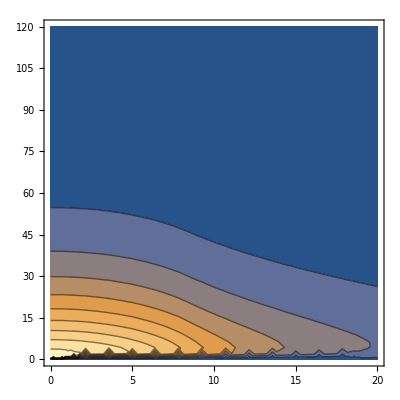

```mathematica
ContourPlot[Evaluate[ATP[r,t]/.pdesolve],{r,0,L plot/20},{t,0,T plot/5},PlotRange->All]
```